# Mean Field Theory for The Four Site Hubbard Model

```mathematica
U = 1.3;
γ=2.1;
```

```mathematica
Clear[Hup]
Hup[z1_,z2_,z3_,z4_]:=({{U z1, γ, 0, γ}, {γ, U z2, γ, 0}, {0, γ, U z3, γ}, {γ, 0, γ, U z4}});
```

```mathematica
Egnup[z1_,z2_,z3_,z4_]:=Eigensystem[Hup[z1,z2,z3,z4]];
```

```mathematica
Hdown[z1_,z2_,z3_,z4_]:=Block[{htp,x1,x2,x3,x4},
{eup,ψup} = Transpose[Sort[Transpose[Egnup[z1,z2,z3,z4]]]];
x1 = Abs[ψup[[1,1]]]^2;
x2 = Abs[ψup[[1,2]]]^2;
x3 = Abs[ψup[[1,3]]]^2;
x4 = Abs[ψup[[1,4]]]^2;
htp = Hup[x1,x2,x3,x4];
htp
];
```

```mathematica
Egndown[z1_,z2_,z3_,z4_]:=Eigensystem[Hdown[z1,z2,z3,z4]];
```

```mathematica
Z[z_]:=Block[{ztp},
{ed,ψd} = Transpose[Sort[Transpose[Egndown[z[[1]],z[[2]],z[[3]],z[[4]]]]]];
ztp = {Abs[ψd[[1,1]]]^2,Abs[ψd[[1,2]]]^2,Abs[ψd[[1,3]]]^2,Abs[ψd[[1,4]]]^2};
ztp
];
```

```mathematica
Z[{0.25,0.25,0.25,0.25}]
```

{0.25,0.25,0.25,0.25}

```mathematica
Clear[Hup,U,γ]
Hup = ({{1/4 U, γ, 0, γ}, {γ, 1/4 U, γ, 0}, {0, γ, 1/4 U, γ}, {γ, 0, γ, 1/4 U}});
Eigenvalues[Hup]
```

{U/4,U/4,1/4 (U-8 γ),1/4 (U+8 γ)}

This was asserting that z_i = |ψ_(1i)|^2 what if we try other eigenstates?

```mathematica
U = 1.3;
γ=2.1;
```

```mathematica
Clear[Hup]
Hup[z1_,z2_,z3_,z4_]:=({{U z1, γ, 0, γ}, {γ, U z2, γ, 0}, {0, γ, U z3, γ}, {γ, 0, γ, U z4}});
```

```mathematica
Egnup[z1_,z2_,z3_,z4_]:=Eigensystem[Hup[z1,z2,z3,z4]];
```

```mathematica
Hdown[n_,z1_,z2_,z3_,z4_]:=Block[{htp,x1,x2,x3,x4},
{eup,ψup} = Transpose[Sort[Transpose[Egnup[z1,z2,z3,z4]]]];
Print["Eup = ",eup[[n]]];
Print["Ψup = ",ψup[[n]]];
x1 = Abs[ψup[[n,1]]]^2;
x2 = Abs[ψup[[n,2]]]^2;
x3 = Abs[ψup[[n,3]]]^2;
x4 = Abs[ψup[[n,4]]]^2;
htp = Hup[x1,x2,x3,x4];
htp
];
```

```mathematica
Egndown[n_,z1_,z2_,z3_,z4_]:=Eigensystem[Hdown[n,z1,z2,z3,z4]];
```

```mathematica
Z[n_,m_,z_]:=Block[{ztp},
{ed,ψd} = Transpose[Sort[Transpose[Egndown[n,z[[1]],z[[2]],z[[3]],z[[4]]]]]];
Print["Edown = ", ed[[m]]];
Print["Ψdown = ",  ψd[[m]]];
ztp = {Abs[ψd[[m,1]]]^2,Abs[ψd[[m,2]]]^2,Abs[ψd[[m,3]]]^2,Abs[ψd[[m,4]]]^2};
ztp
];
```

```mathematica
Z[2,2,{0.0,0.5,0.0,0.5}]
```

Eup = 0.

Ψup = {0.707107,0.,-0.707107,0.}

Edown = 5.32907×10^-15

Ψdown = {-6.24892×10^-16,-0.707107,-5.71368×10^-16,0.707107}

{3.90491×10^-31,0.5,3.26462×10^-31,0.5}

```mathematica
Clear[Hup,U,γ]
Hup = ({{U 0, γ, 0, γ}, {γ, 1/2 U, γ, 0}, {0, γ, U 0, γ}, {γ, 0, γ, 1/2 U}});
Eigenvalues[Hup]
```

{0,U/2,1/4 (U-√(U^2+64 γ^2)),1/4 (U+√(U^2+64 γ^2))}

```mathematica
Eigenvectors[Hup]
```

{{-1,0,1,0},{0,-1,0,1},{-(U+√(U^2+64 γ^2))/(8 γ),1,-(U+√(U^2+64 γ^2))/(8 γ),1},{-(U-√(U^2+64 γ^2))/(8 γ),1,-(U-√(U^2+64 γ^2))/(8 γ),1}}

```mathematica
Hup.{-1,0,1,0}
```

{0,0,0,0}

This only works for the E = 0 eigenvalue.  I think there should be another one somewhere.

```mathematica
Clear[Hup,U,γ]
Hup = ({{U, γ, 0, γ}, {γ, U, γ, 0}, {0, γ, U, γ}, {γ, 0, γ, U}});
```

Let’s take a look at all of these energy levels

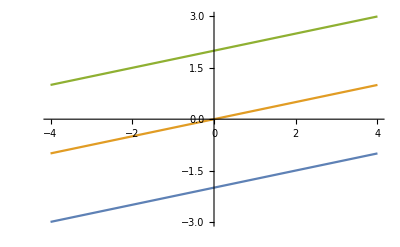

```mathematica
γ=1.0;
E0[U_]:=1/4 U-2 γ
Ea[U_]:=1/4 U
E1[U_]:=1/4 (U-√(U^2+16 γ^2))
E2[U_]:=1/4 (U+√(U^2+16 γ^2))
E3[U_]:=1/4 U+2 γ
Eb[U_]:=1/2 U
Ec[U_]:=0

Plot[{E0[U],Ea[U],E3[U]},{U,-4,4}]
```

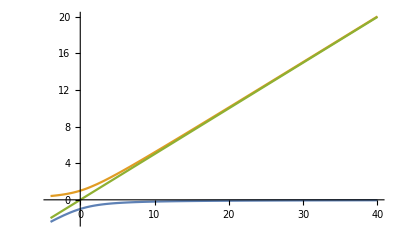

```mathematica
Plot[{E1[U],E2[U],Eb[U],Ec(U)},{U,-4,40}]
```

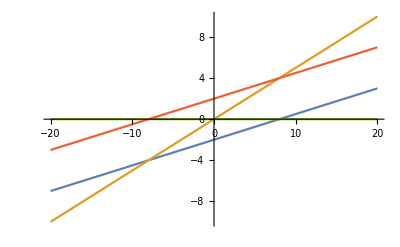

```mathematica
Plot[{E0[U],Eb[U],Ec[U],E3[U]},{U,-20,20}]
```